## Energy Function - Contour Plots

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

```mathematica
Tcore[I_,A1_,A2_,A3_]:=I/2(A1+A2)+A3*I^2;
Tsp[j_,A1_,A2_,A3_,V_,gm_]:=j/2(A2+A3)+A1*j^2-V*(2j-1)/(j+1)Sin[gm*π/180+π/6];
Aphi[phi_,A1_,A2_,A3_]:=A1*Cos[phi]^2+A2*Sin[phi]^2-A3;
Hmin[theta_,phi_,I_,j_,A1_,A2_,A3_,V_,gm_]:=I(I-1/2)Sin[theta]^2*Aphi[phi,A1,A2,A3]-2*A1*I*j*Sin[theta]+Tcore[I,A1,A2,A3]+Tsp[j,A1,A2,A3,V,gm];
Ak[moi_]:=1/(2*moi);
```

```mathematica
I1fit=72;I2fit=15;I3fit=7;
Vfit=2.1;gmfit=22;
j1=13/2;
A1fit=Ak[I1fit];A2fit=Ak[I2fit];A3fit=Ak[I3fit];
Hpolar[theta_,phi_,I_]:=Hmin[theta,phi,I,j1,A1fit,A2fit,A3fit,Vfit,gmfit];
```

### Contour plots

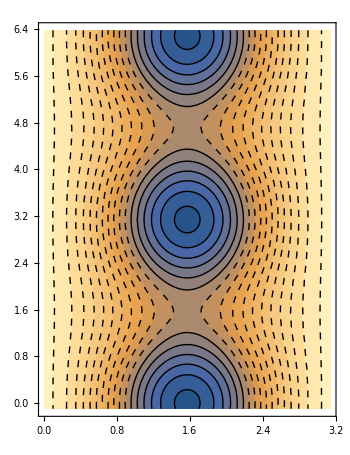

```mathematica
(* Set style for range of contours *)
(* source: https://mathematica.stackexchange.com/questions/28762/contourstyle-for-a-particular-contour-line-in-contourplot *)
texStyle={FontFamily->"Latin Modern Roman",FontSize->18};
cp[I_]:=ContourPlot[Hpolar[θ,φ,I],{θ,0,π},{φ,-0.1,2π+0.1},AspectRatio->1.3,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->MaTeX/@{"\\theta\\ [\\text{rad}]","\\varphi\\ [\\text{rad}]"},ImageSize->350,Contours->({#,If[#>=2.5,Directive[Dashed,Black],Directive[Black] ]}&/@Range[-100,100,0.65]),PlotRangePadding->None,BaseStyle->texStyle];
Show[cp[25/2]]
```